```mathematica
SetDirectory @ NotebookDirectory[];
<<Rotation.m
<<Linearize.m
<<PlotCustom.m
<<NotationRules.m
```

-Graphics-

Coordenadas Generalizadas

```mathematica
q[t_] = {q0[t],q1[t], q2[t], q3[t]}
v[t_] = {wx[t],wy[t], wz[t]}
x[t_] = {q0[t], q1[t], q2[t],q3[t],wx[t],wy[t], wz[t]};
u[t_] = {taux[t], tauy[t], tauz[t]}
y[t_] = {wx[t],wy[t], wz[t]}
rep = {l-> 0.15, ms->0.4, mrr->0.15, Js -> 2/1000, Jrra -> 1.25/10000, Jrrrad -> 4/100000, g->9.81, mc->0.55, b->17.03*10^(-6)}
```

{q0[t],q1[t],q2[t],q3[t]}

{wx[t],wy[t],wz[t]}

{taux[t],tauy[t],tauz[t]}

{wx[t],wy[t],wz[t]}

{l→0.15,ms→0.4,mrr→0.15,Js→1/500,Jrra→0.000125,Jrrrad→1/25000,g→9.81,3 mrr+ms→0.55,b→0.00001703}

Vetor velocidade do Referencial .08Móvel

```mathematica
Subscript[ω, c] = v[t]
```

{wx[t],wy[t],wz[t]}

```mathematica
{wx[t],wy[t],wz[t]}
```

{wx[t],wy[t],wz[t]}

Modelagem Cinemática

```mathematica
G = {{-q1[t], q0[t], q3[t], -q2[t]},{-q2[t], -q3[t], q0[t], q1[t]},{-q3[t],q2[t], -q1[t], q0[t]}}
G //MatrixForm 

quatd = (1/2)*Transpose[G].Subscript[ω, c] //FullSimplify
quatd //MatrixForm

ce = Solve[{quatd == q'[t]}, q'[t]] // First // FullSimplify
ce //TableForm
```

{{-q1[t],q0[t],q3[t],-q2[t]},{-q2[t],-q3[t],q0[t],q1[t]},{-q3[t],q2[t],-q1[t],q0[t]}}

(-q1[t] | q0[t] | q3[t] | -q2[t]
-q2[t] | -q3[t] | q0[t] | q1[t]
-q3[t] | q2[t] | -q1[t] | q0[t])

{1/2 (-q1[t] wx[t]-q2[t] wy[t]-q3[t] wz[t]),1/2 (q0[t] wx[t]-q3[t] wy[t]+q2[t] wz[t]),1/2 (q3[t] wx[t]+q0[t] wy[t]-q1[t] wz[t]),1/2 (-q2[t] wx[t]+q1[t] wy[t]+q0[t] wz[t])}

(1/2 (-q1[t] wx[t]-q2[t] wy[t]-q3[t] wz[t])
1/2 (q0[t] wx[t]-q3[t] wy[t]+q2[t] wz[t])
1/2 (q3[t] wx[t]+q0[t] wy[t]-q1[t] wz[t])
1/2 (-q2[t] wx[t]+q1[t] wy[t]+q0[t] wz[t]))

{q0'[t]→1/2 (-q1[t] wx[t]-q2[t] wy[t]-q3[t] wz[t]),q1'[t]→1/2 (q0[t] wx[t]-q3[t] wy[t]+q2[t] wz[t]),q2'[t]→1/2 (q3[t] wx[t]+q0[t] wy[t]-q1[t] wz[t]),q3'[t]→1/2 (-q2[t] wx[t]+q1[t] wy[t]+q0[t] wz[t])}

q0'[t]→1/2 (-q1[t] wx[t]-q2[t] wy[t]-q3[t] wz[t])
q1'[t]→1/2 (q0[t] wx[t]-q3[t] wy[t]+q2[t] wz[t])
q2'[t]→1/2 (q3[t] wx[t]+q0[t] wy[t]-q1[t] wz[t])
q3'[t]→1/2 (-q2[t] wx[t]+q1[t] wy[t]+q0[t] wz[t])

Dinâmica

```mathematica
J=.

Subscript[r, rr1] = {0, l/2, l/2};
Subscript[r, rr2]={l/2, 0, l/2};
Subscript[r, rr3]={l/2, l/2, 0};
Subscript[r, s]= {l/2, l/2, l/2};
mc= ms + 3*mrr;
Subscript[r, c] = (ms*Subscript[r, s] + mrr*(Subscript[r, rr1] + Subscript[r, rr2] + Subscript[r, rr3]))/(ms+3*mrr);

Subscript[r, c]/.rep
Subscript[𝕀^O, rrx] = {{Jrra + mrr*l^2/2, 0, 0}, {0,Jrrrad + mrr*l^2/4,-mrr*l^2/4},{0,-mrr*l^2/4,Jrrrad + mrr*l^2/4}};
Subscript[𝕀^O, rry] = {{Jrrrad + mrr*l^2/4, 0, -mrr*l^2/4}, {0,Jrra + mrr*l^2/2,0},{-mrr*l^2/4,0,Jrrrad + mrr*l^2/4}};
Subscript[𝕀^O, rrz] = {{Jrrrad + mrr*l^2/4, -mrr*l^2/4, 0}, {-mrr*l^2/4,Jrrrad + mrr*l^2/4,0},{0,0,Jrra + mrr*l^2/2}};
Subscript[𝕀^O, s] = {{Js + ms*l^2/2, -ms*l^2/4, -ms*l^2/4},{-ms*l^2/4, Js + ms*l^2/2,-ms*l^2/4},{-ms*l^2/4,-ms*l^2/4,Js + ms*l^2/2}};
Subscript[𝕀^O1, c] = Subscript[𝕀^O, s] + Subscript[𝕀^O, rrz] + Subscript[𝕀^O, rrx] + Subscript[𝕀^O, rry]
Subscript[𝕀^O1, c]/.rep //MatrixForm
EIG = Eigenvalues[Subscript[𝕀^O1, c]]
EIGVEC = Eigenvectors[Subscript[𝕀^O1, c]]
EIGVEC //MatrixForm
Subscript[𝕀^O, c] = {{EIG[[2]],0,0},{0,EIG[[3]],0},{0,0,EIG[[1]]}}
Subscript[𝕀^O, c]/.rep //TableForm
λ = {{0,0,0,1},{0,0,1,0},{0,-1,0,0},{-1,0,0,0}};


tau = u[t];
qtil = {{0, -q3[t], q2[t]},{q3[t], 0, -q1[t]},{-q2[t], q1[t], 0}};
qvec = {q1[t],q2[t],q3[t]};
gvec = {0,0,g};
gline= 2*(qvec.gvec)*qvec + q0[t]^2*gvec+ 2*q0[t]*(Cross[gvec,qvec]) - qvec.qvec*gvec;
Subscript[H, O] =Subscript[𝕀^O, c].Subscript[ω, c] //FullSimplify;
M = tau + mc*Cross[gline, Subscript[r, c]] -b*(G.λ.q[t].Transpose[G.λ.q[t]])*Subscript[ω, c] //FullSimplify;
M //TableForm


TQMA = (D[Subscript[H, O], t]) + Cross[Subscript[ω, c],Subscript[H, O]] - M  //FullSimplify
TQMA /.notation//TableForm
```

{0.0954545,0.0954545,0.0954545}

{{Jrra+2 Jrrrad+Js+l^2 mrr+(l^2 ms)/2,-(l^2 mrr)/4-(l^2 ms)/4,-(l^2 mrr)/4-(l^2 ms)/4},{-(l^2 mrr)/4-(l^2 ms)/4,Jrra+2 Jrrrad+Js+l^2 mrr+(l^2 ms)/2,-(l^2 mrr)/4-(l^2 ms)/4},{-(l^2 mrr)/4-(l^2 ms)/4,-(l^2 mrr)/4-(l^2 ms)/4,Jrra+2 Jrrrad+Js+l^2 mrr+(l^2 ms)/2}}

(0.01008 | -0.00309375 | -0.00309375
-0.00309375 | 0.01008 | -0.00309375
-0.00309375 | -0.00309375 | 0.01008)

{1/2 (2 Jrra+4 Jrrrad+2 Js+l^2 mrr),1/4 (4 Jrra+8 Jrrrad+4 Js+5 l^2 mrr+3 l^2 ms),1/4 (4 Jrra+8 Jrrrad+4 Js+5 l^2 mrr+3 l^2 ms)}

{{1,1,1},{-1,0,1},{-1,1,0}}

(1 | 1 | 1
-1 | 0 | 1
-1 | 1 | 0)

{{1/4 (4 Jrra+8 Jrrrad+4 Js+5 l^2 mrr+3 l^2 ms),0,0},{0,1/4 (4 Jrra+8 Jrrrad+4 Js+5 l^2 mrr+3 l^2 ms),0},{0,0,1/2 (2 Jrra+4 Jrrrad+2 Js+l^2 mrr)}}

0.0131738 | 0 | 0
0 | 0.0131738 | 0
0 | 0 | 0.0038925

-1/2 g l (2 mrr+ms) (q0[t]^2-2 q0[t] q1[t]-q1[t]^2-q2[t]^2-2 q2[t] q3[t]+q3[t]^2)+taux[t]-b (q0[t]^2+q1[t]^2+q2[t]^2+q3[t]^2)^2 wx[t]
1/2 g l (2 mrr+ms) (q0[t]^2-q1[t]^2+2 q0[t] q2[t]-q2[t]^2-2 q1[t] q3[t]+q3[t]^2)+tauy[t]-b (q0[t]^2+q1[t]^2+q2[t]^2+q3[t]^2)^2 wy[t]
-g l (2 mrr+ms) (q0[t] (q1[t]+q2[t])+(-q1[t]+q2[t]) q3[t])+tauz[t]-b (q0[t]^2+q1[t]^2+q2[t]^2+q3[t]^2)^2 wz[t]

{1/4 (2 g l (2 mrr+ms) (q0[t]^2-2 q0[t] q1[t]-q1[t]^2-q2[t]^2-2 q2[t] q3[t]+q3[t]^2)-4 taux[t]+4 b (q0[t]^2+q1[t]^2+q2[t]^2+q3[t]^2)^2 wx[t]-3 l^2 mrr wy[t] wz[t]-3 l^2 ms wy[t] wz[t]+(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms)) wx'[t]),1/4 (-2 g l (2 mrr+ms) (q0[t]^2-q1[t]^2+2 q0[t] q2[t]-q2[t]^2-2 q1[t] q3[t]+q3[t]^2)-4 tauy[t]+4 b (q0[t]^2+q1[t]^2+q2[t]^2+q3[t]^2)^2 wy[t]+3 l^2 mrr wx[t] wz[t]+3 l^2 ms wx[t] wz[t]+(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms)) wy'[t]),g l (2 mrr+ms) (q0[t] (q1[t]+q2[t])+(-q1[t]+q2[t]) q3[t])-tauz[t]+b (q0[t]^2+q1[t]^2+q2[t]^2+q3[t]^2)^2 wz[t]+1/2 (2 (Jrra+2 Jrrrad+Js)+l^2 mrr) wz'[t]}

1/4 (2 g l (2 mrr+ms) (q0^2-2 q0 q1-q1^2-q2^2-2 q2 q3+q3^2)-4 taux+4 b (q0^2+q1^2+q2^2+q3^2)^2 wx-3 l^2 mrr wy wz-3 l^2 ms wy wz+(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms)) OverDot[wx])
1/4 (-2 g l (2 mrr+ms) (q0^2-q1^2+2 q0 q2-q2^2-2 q1 q3+q3^2)-4 tauy+4 b (q0^2+q1^2+q2^2+q3^2)^2 wy+3 l^2 mrr wx wz+3 l^2 ms wx wz+(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms)) OverDot[wy])
g l (2 mrr+ms) (q0 (q1+q2)+(-q1+q2) q3)-tauz+b (q0^2+q1^2+q2^2+q3^2)^2 wz+1/2 (2 (Jrra+2 Jrrrad+Js)+l^2 mrr) OverDot[wz]

Equações Diferenciais

```mathematica
{m𝔽, 𝕄} = Normal @ CoefficientArrays[TQMA, v'[t]] ;
𝕄 // MatrixForm (*Matriz de inércia generalizda*)
𝔽 = -m𝔽 // FullSimplify;
𝔽 // MatrixForm (*Vetor de forças generalizadas*)
```

(1/4 (4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms)) | 0 | 0
0 | 1/4 (4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms)) | 0
0 | 0 | 1/2 (2 (Jrra+2 Jrrrad+Js)+l^2 mrr))

(-1/2 g l (2 mrr+ms) (q0[t]^2-2 q0[t] q1[t]-q1[t]^2-q2[t]^2-2 q2[t] q3[t]+q3[t]^2)+taux[t]-b (q0[t]^2+q1[t]^2+q2[t]^2+q3[t]^2)^2 wx[t]+3/4 l^2 mrr wy[t] wz[t]+3/4 l^2 ms wy[t] wz[t]
1/2 g l (2 mrr+ms) (q0[t]^2-q1[t]^2+2 q0[t] q2[t]-q2[t]^2-2 q1[t] q3[t]+q3[t]^2)+tauy[t]-b (q0[t]^2+q1[t]^2+q2[t]^2+q3[t]^2)^2 wy[t]-3/4 l^2 mrr wx[t] wz[t]-3/4 l^2 ms wx[t] wz[t]
-g l (2 mrr+ms) (q0[t] (q1[t]+q2[t])+(-q1[t]+q2[t]) q3[t])+tauz[t]-b (q0[t]^2+q1[t]^2+q2[t]^2+q3[t]^2)^2 wz[t])

Equações de Movimento

```mathematica
EOMa[t_] = Flatten @ Solve[
	(# == 0)& /@ TQMA,
	v'[t]
	] // Collect[#, v[t], FullSimplify]&;
EOMa[t] // TableForm
```

wx'[t]→(-2 g l (2 mrr+ms) (q0[t]^2-2 q0[t] q1[t]-q1[t]^2-q2[t]^2-2 q2[t] q3[t]+q3[t]^2)+4 taux[t])/(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms))-(4 b (q0[t]^2+q1[t]^2+q2[t]^2+q3[t]^2)^2 wx[t])/(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms))+(3 l^2 (mrr+ms) wy[t] wz[t])/(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms))
wy'[t]→(2 g l (2 mrr+ms) (q0[t]^2-q1[t]^2+2 q0[t] q2[t]-q2[t]^2-2 q1[t] q3[t]+q3[t]^2)+4 tauy[t])/(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms))-(4 b (q0[t]^2+q1[t]^2+q2[t]^2+q3[t]^2)^2 wy[t])/(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms))-(3 l^2 (mrr+ms) wx[t] wz[t])/(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms))
wz'[t]→(2 (-g l (2 mrr+ms) (q0[t] (q1[t]+q2[t])+(-q1[t]+q2[t]) q3[t])+tauz[t]))/(2 (Jrra+2 Jrrrad+Js)+l^2 mrr)-(2 b (q0[t]^2+q1[t]^2+q2[t]^2+q3[t]^2)^2 wz[t])/(2 (Jrra+2 Jrrrad+Js)+l^2 mrr)

FORMA DE ESPAÇO DE ESTADOS

```mathematica
𝕗 = (x'[t]/.ce/.EOMa[t]);
𝕗 // TableForm
𝕗 /.rep // TableForm
```

1/2 (-q1[t] wx[t]-q2[t] wy[t]-q3[t] wz[t])
1/2 (q0[t] wx[t]-q3[t] wy[t]+q2[t] wz[t])
1/2 (q3[t] wx[t]+q0[t] wy[t]-q1[t] wz[t])
1/2 (-q2[t] wx[t]+q1[t] wy[t]+q0[t] wz[t])
(-2 g l (2 mrr+ms) (q0[t]^2-2 q0[t] q1[t]-q1[t]^2-q2[t]^2-2 q2[t] q3[t]+q3[t]^2)+4 taux[t])/(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms))-(4 b (q0[t]^2+q1[t]^2+q2[t]^2+q3[t]^2)^2 wx[t])/(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms))+(3 l^2 (mrr+ms) wy[t] wz[t])/(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms))
(2 g l (2 mrr+ms) (q0[t]^2-q1[t]^2+2 q0[t] q2[t]-q2[t]^2-2 q1[t] q3[t]+q3[t]^2)+4 tauy[t])/(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms))-(4 b (q0[t]^2+q1[t]^2+q2[t]^2+q3[t]^2)^2 wy[t])/(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms))-(3 l^2 (mrr+ms) wx[t] wz[t])/(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms))
(2 (-g l (2 mrr+ms) (q0[t] (q1[t]+q2[t])+(-q1[t]+q2[t]) q3[t])+tauz[t]))/(2 (Jrra+2 Jrrrad+Js)+l^2 mrr)-(2 b (q0[t]^2+q1[t]^2+q2[t]^2+q3[t]^2)^2 wz[t])/(2 (Jrra+2 Jrrrad+Js)+l^2 mrr)

1/2 (-q1[t] wx[t]-q2[t] wy[t]-q3[t] wz[t])
1/2 (q0[t] wx[t]-q3[t] wy[t]+q2[t] wz[t])
1/2 (q3[t] wx[t]+q0[t] wy[t]-q1[t] wz[t])
1/2 (-q2[t] wx[t]+q1[t] wy[t]+q0[t] wz[t])
18.9771 (-2.0601 (q0[t]^2-2 q0[t] q1[t]-q1[t]^2-q2[t]^2-2 q2[t] q3[t]+q3[t]^2)+4 taux[t])-0.00129272 (q0[t]^2+q1[t]^2+q2[t]^2+q3[t]^2)^2 wx[t]+0.704526 wy[t] wz[t]
18.9771 (2.0601 (q0[t]^2-q1[t]^2+2 q0[t] q2[t]-q2[t]^2-2 q1[t] q3[t]+q3[t]^2)+4 tauy[t])-0.00129272 (q0[t]^2+q1[t]^2+q2[t]^2+q3[t]^2)^2 wy[t]-0.704526 wx[t] wz[t]
256.904 (-1.03005 (q0[t] (q1[t]+q2[t])+(-q1[t]+q2[t]) q3[t])+tauz[t])-0.00437508 (q0[t]^2+q1[t]^2+q2[t]^2+q3[t]^2)^2 wz[t]

```mathematica
RP = {q1[t]->0, q2[t]->0 ,q3[t]->0,wx[t]->0,wy[t]->0, wz[t]->0}
```

{q1[t]→0,q2[t]→0,q3[t]→0,wx[t]→0,wy[t]→0,wz[t]→0}

```mathematica
TQMAL=.
𝕩L[t_] = {q1[t], q2[t],q3[t],wx[t],wy[t], wz[t]};
𝕪L[t_] = {wx[t],wy[t], wz[t]};
TQMAL = Linearize[TQMA/.{q0[t]->Sqrt[1-q1[t]^2-q2[t]^2-q3[t]^2]}, RP] //Simplify

EOML[t_] = Flatten @ Solve[
	(# == 0)& /@ TQMAL,
	v'[t]
	] // Collect[#, v[t], FullSimplify]&



quatL = Linearize[quatd/.{q0[t] -> Sqrt[1-q1[t]^2-q2[t]^2-q3[t]^2]},RP]
ceL = Solve[{quatL == q'[t]}, q'[t]] // First // FullSimplify
```

{1/4 (2 g l (2 mrr+ms)-4 g l (2 mrr+ms) q1[t]-4 taux[t]+4 b wx[t]+(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms)) wx'[t]),1/4 (-2 g l (2 mrr+ms)-4 g l (2 mrr+ms) q2[t]-4 tauy[t]+4 b wy[t]+(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms)) wy'[t]),g l (2 mrr+ms) (q1[t]+q2[t])-tauz[t]+b wz[t]+1/2 (2 (Jrra+2 Jrrrad+Js)+l^2 mrr) wz'[t]}

{wx'[t]→(2 g l (2 mrr+ms) (-1+2 q1[t])+4 taux[t])/(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms))-(4 b wx[t])/(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms)),wy'[t]→(2 g l (2 mrr+ms) (1+2 q2[t])+4 tauy[t])/(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms))-(4 b wy[t])/(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms)),wz'[t]→(-2 g l (2 mrr+ms) (q1[t]+q2[t])+2 tauz[t])/(2 (Jrra+2 Jrrrad+Js)+l^2 mrr)-(2 b wz[t])/(2 (Jrra+2 Jrrrad+Js)+l^2 mrr)}

{0,wx[t]/2,wy[t]/2,wz[t]/2}

{q0'[t]→0,q1'[t]→wx[t]/2,q2'[t]→wy[t]/2,q3'[t]→wz[t]/2}

Espaço de Estados Linearizado

```mathematica
𝕗L = (𝕩L'[t]/.ceL/.EOML[t]);
𝕗L // TableForm
𝕗L /. rep //TableForm
```

wx[t]/2
wy[t]/2
wz[t]/2
(2 g l (2 mrr+ms) (-1+2 q1[t])+4 taux[t])/(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms))-(4 b wx[t])/(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms))
(2 g l (2 mrr+ms) (1+2 q2[t])+4 tauy[t])/(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms))-(4 b wy[t])/(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms))
(-2 g l (2 mrr+ms) (q1[t]+q2[t])+2 tauz[t])/(2 (Jrra+2 Jrrrad+Js)+l^2 mrr)-(2 b wz[t])/(2 (Jrra+2 Jrrrad+Js)+l^2 mrr)

wx[t]/2
wy[t]/2
wz[t]/2
18.9771 (2.0601 (-1+2 q1[t])+4 taux[t])-0.00129272 wx[t]
18.9771 (2.0601 (1+2 q2[t])+4 tauy[t])-0.00129272 wy[t]
128.452 (-2.0601 (q1[t]+q2[t])+2 tauz[t])-0.00437508 wz[t]

Determinação da matriz A

```mathematica
𝔸1 = CoefficientArrays[𝕗L, 𝕩L[t]][[2]] // Normal;
 𝔸1 //FullSimplify // MatrixForm
 
 𝔸=N[𝔸1/.rep] //FullSimplify; 
 𝔸 //MatrixForm
 Eigenvalues[𝔸]
```

(0 | 0 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 1/2
(4 g l (2 mrr+ms))/(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms)) | 0 | 0 | -(4 b)/(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms)) | 0 | 0
0 | (4 g l (2 mrr+ms))/(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms)) | 0 | 0 | -(4 b)/(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms)) | 0
-(2 g l (2 mrr+ms))/(2 (Jrra+2 Jrrrad+Js)+l^2 mrr) | -(2 g l (2 mrr+ms))/(2 (Jrra+2 Jrrrad+Js)+l^2 mrr) | 0 | 0 | 0 | -(2 b)/(2 (Jrra+2 Jrrrad+Js)+l^2 mrr))

(0. | 0. | 0. | 0.5 | 0. | 0.
0. | 0. | 0. | 0. | 0.5 | 0.
0. | 0. | 0. | 0. | 0. | 0.5
78.1896 | 0. | 0. | -0.00129272 | 0. | 0.
0. | 78.1896 | 0. | 0. | -0.00129272 | 0.
-264.624 | -264.624 | 0. | 0. | 0. | -0.00437508)

{-6.25323,-6.25323,6.25194,6.25194,-0.00437508,0.}

Determinação  das matrizes B, C e D

```mathematica
𝔹1 = CoefficientArrays[𝕗L, u[t]][[2]] // Normal;
𝔹1 //FullSimplify //MatrixForm
𝔹=N[𝔹1/.rep] //FullSimplify;
𝔹//MatrixForm

ℂ1 = CoefficientArrays[𝕪L[t], 𝕩L[t]][[2]] // Normal;
ℂ1 //FullSimplify //MatrixForm
ℂ=N[ℂ1/.rep] //FullSimplify; 
ℂ//MatrixForm
𝔻 = ConstantArray[0, {3, 3}]
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
4/(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms)) | 0 | 0
0 | 4/(4 Jrra+8 Jrrrad+4 Js+l^2 (5 mrr+3 ms)) | 0
0 | 0 | 2/(2 (Jrra+2 Jrrrad+Js)+l^2 mrr))

(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.
75.9085 | 0. | 0.
0. | 75.9085 | 0.
0. | 0. | 256.904)

(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

(0. | 0. | 0. | 1. | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 1.)

{{0,0,0},{0,0,0},{0,0,0}}

Transfer Function

StateSpaceModel[{{{0.,0.,0.,0.5,0.,0.},{0.,0.,0.,0.,0.5,0.},{0.,0.,0.,0.,0.,0.5},{78.1896,0.,0.,-0.00129272,0.,0.},{0.,78.1896,0.,0.,-0.00129272,0.},{-264.624,-264.624,0.,0.,0.,-0.00437508}},{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{75.9085,0.,0.},{0.,75.9085,0.},{0.,0.,256.904}},{{0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,1.}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}}]

TransferFunctionModel::invsys: StateSpaceModel[{{{0.,0.,0.,0.5,0.,0.},{0.,0.,0.,0.,0.5,0.},{0.,0.,0.,0.,0.,0.5},{78.1896,0.,0.,-0.00129272,0.,0.},{0.,78.1896,0.,0.,-0.00129272,0.},{-264.624,-264.624,0.,0.,0.,-0.00437508}},{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{75.9085,0.,0.},{0.,75.9085,0.},{0.,0.,256.904}},{{0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,1.}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}}] is not a valid TransferFunctionModel, StateSpaceModel, AffineStateSpaceModel, or NonlinearStateSpaceModel.

TransferFunctionModel[StateSpaceModel[{{{0.,0.,0.,0.5,0.,0.},{0.,0.,0.,0.,0.5,0.},{0.,0.,0.,0.,0.,0.5},{78.1896,0.,0.,-0.00129272,0.,0.},{0.,78.1896,0.,0.,-0.00129272,0.},{-264.624,-264.624,0.,0.,0.,-0.00437508}},{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{75.9085,0.,0.},{0.,75.9085,0.},{0.,0.,256.904}},{{0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,1.}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}}],s]

SystemsModelDimensions::invsys: TransferFunctionModel[StateSpaceModel[{{{0.,0.,0.,0.5,0.,0.},{0.,0.,0.,0.,0.5,0.},{0.,0.,0.,0.,0.,0.5},{78.1896,0.,0.,-0.00129272,0.,0.},{0.,78.1896,0.,0.,-0.00129272,0.},{-264.624,-264.624,0.,0.,0.,-0.00437508}},{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{75.9085,0.,0.},{0.,75.9085,0.},{0.,0.,256.904}},{{0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,1.}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}}],s] is not a valid TransferFunctionModel, StateSpaceModel, AffineStateSpaceModel, or NonlinearStateSpaceModel.

Array::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ….

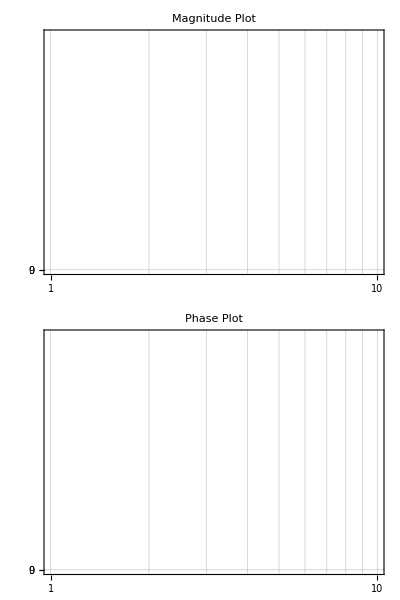

TransferFunctionPoles::invtf: TransferFunctionModel[StateSpaceModel[{{{0.,0.,0.,0.5,0.,0.},{0.,0.,0.,0.,0.5,0.},{0.,0.,0.,0.,0.,0.5},{78.1896,0.,0.,-0.00129272,0.,0.},{0.,78.1896,0.,0.,-0.00129272,0.},{-264.624,-264.624,0.,0.,0.,-0.00437508}},{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{75.9085,0.,0.},{0.,75.9085,0.},{0.,0.,256.904}},{{0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,1.}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}}],s] is not a valid TransferFunctionModel object.

TransferFunctionPoles[TransferFunctionModel[StateSpaceModel[{{{0.,0.,0.,0.5,0.,0.},{0.,0.,0.,0.,0.5,0.},{0.,0.,0.,0.,0.,0.5},{78.1896,0.,0.,-0.00129272,0.,0.},{0.,78.1896,0.,0.,-0.00129272,0.},{-264.624,-264.624,0.,0.,0.,-0.00437508}},{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{75.9085,0.,0.},{0.,75.9085,0.},{0.,0.,256.904}},{{0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,1.}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}}],s]]

```mathematica
𝕊 = StateSpaceModel[{𝔸,𝔹,ℂ,𝔻}]

𝕋 = TransferFunctionModel[𝕊,s]


BodePlot[𝕋, PlotTheme->"Scientific", GridLines->Automatic, PlotStyle->100, PlotLabel->{"Magnitude Plot","Phase Plot"}]



p = TransferFunctionPoles[𝕋]
```

```mathematica
Unprotect[Power];
Format[Power[a_,n_Integer],CForm]:=Distribute[ConstantArray[Hold[a],n],Hold,List,HoldForm,Times]
Protect[Power];
crule = MapThread[#1->#2&, {#, y/@((Range[Length@#]))}& @ x[t]];
csorule = {"Cos"->"cos", "Sin"->"sin", "Tan"->"tan", "Sec"->"sec"};
csqrule = {};

fileD = OpenWrite["state_space_cubli.m"];
(*WriteString[fileD, (#/.(({ii_}->vv_):>(StringReplace[StringReplace[ToString @ StringForm["dy(``) = ``;", ii, (vv /. crule //CForm)], csqrule], csorule]<>"\n")))]&/@ (Normal@(Select[#,Not @(NumericQ[#])&]&@Association@Delete[ArrayRules@SparseArray[(y'[t]/.EOM[t])], -1]));*)
WriteString[fileD, (#/.(({ii_}->vv_):>(StringReplace[StringReplace[ToString @ StringForm["    ``;", (vv /. crule //CForm)], csqrule], csorule]<>"\n")))]&/@ (Normal@(Select[#,Not @(NumericQ[#])&]&@Association@Delete[ArrayRules@SparseArray[(𝕩L'[t]/.ceL/.EOML[t])], -1]));
WriteString[fileD, "\n"];
Close[fileD];
```